# DatabaseLink Tutorial

## Getting Started

```mathematica
Needs["DatabaseLink`"]
```

```mathematica
conn=OpenSQLConnection["demo"]
```

SQLConnection[…]

```mathematica
conn1=OpenSQLConnection[];
```

```mathematica
SQLTables[conn]
```

{SQLTable[SAMPLETABLE1,TableType→TABLE]}

```mathematica
SQLColumns[conn,"SAMPLETABLE1"]
```

{SQLColumn[{SAMPLETABLE1,ENTRY},DataTypeName→INTEGER,DataLength→32,Default→Null,Nullable→1],SQLColumn[{SAMPLETABLE1,VALUE},DataTypeName→DOUBLE,DataLength→64,Default→Null,Nullable→1],SQLColumn[{SAMPLETABLE1,NAME},DataTypeName→VARCHAR,DataLength→16,Default→Null,Nullable→1]}

```mathematica
data=SQLSelect[conn,"SAMPLETABLE1"]
```

{{1,5.6,Day1},{2,5.9,Day2},{3,7.2,Day3},{4,6.2,Day4},{5,6.,Day5}}

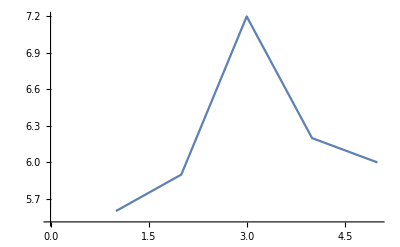

```mathematica
ListLinePlot[data[[All,2]]]
```

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]
```

{{ENTRY,VALUE,NAME},{1,5.6,Day1},{2,5.9,Day2},{3,7.2,Day3},{4,6.2,Day4},{5,6.,Day5}}

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2
3 | 7.2 | Day3
4 | 6.2 | Day4
5 | 6. | Day5

```mathematica
SQLExecute[conn,"SELECT * FROM SAMPLETABLE1"]
```

{{1,5.6,Day1},{2,5.9,Day2},{3,7.2,Day3},{4,6.2,Day4},{5,6.,Day5}}

## Inserting Data

```mathematica
SQLInsert[conn,"SAMPLETABLE1",{"ENTRY","VALUE","NAME"},{6,8.2,"Day6"}]
```

1

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2
3 | 7.2 | Day3
4 | 6.2 | Day4
5 | 6. | Day5
6 | 8.2 | dAY6
6 | 8.2 | Day6

```mathematica
SQLExecute[conn,"INSERT INTO SAMPLETABLE1(ENTRY, VALUE, NAME) VALUES (7,6.9,'Day7')"]
```

1

```mathematica
SQLExecute[conn,"INSERT INTO SAMPLETABLE1 (ENTRY, VALUE, NAME) VALUES (`1`,`2`,`3`)",{8,10.5,"Day8"}]
```

1

```mathematica
SQLExecute[conn,"SELECT * FROM SAMPLETABLE1"]
```

{{1,5.6,Day1},{2,5.9,Day2},{3,7.2,Day3},{4,6.2,Day4},{5,6.,Day5},{6,8.2,dAY6},{6,8.2,Day6},{7,6.9,Day7},{8,10.5,Day8}}

## Updating Data

```mathematica
SQLUpdate[conn,"SAMPLETABLE1",{"VALUE"},{7},SQLColumn["Value"]>8]
```

0

```mathematica
SQLUpdate[conn,"SAMPLETABLE1",{"VALUE"},{7},SQLColumn["VALUE"]>8]
```

3

```mathematica
SQLSelect[conn,"SAMPLETABLE1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2
3 | 7.2 | Day3
4 | 6.2 | Day4
5 | 6. | Day5
7 | 6.9 | Day7
6 | 7. | dAY6
6 | 7. | Day6
8 | 7. | Day8

```mathematica
SQLExecute[conn,"update sampletable1 set value = `1` where value >=`2`",{7,6}]
```

7

```mathematica
SQLExecute[conn,"select * from sampletable1"]
```

{{1,5.6,Day1},{2,5.9,Day2},{3,7.,Day3},{4,7.,Day4},{5,7.,Day5},{7,7.,Day7},{6,7.,dAY6},{6,7.,Day6},{8,7.,Day8}}

## Deleting Data

```mathematica
SQLDelete[conn,"Sampletable1",SQLColumn["value"]>=7]
```

7

```mathematica
SQLSelect[conn,"Sampletable1","ShowColumnHeadings"->True]//TableForm
```

ENTRY | VALUE | NAME
1 | 5.6 | Day1
2 | 5.9 | Day2

```mathematica
SQLExecute[conn,"select * from sampletable1"]
```

{{1,5.6,Day1},{2,5.9,Day2}}

```mathematica
SQLExecute[conn,"delete from sampletable1 where value>=5.7"]
```

1

```mathematica
SQLExecute[conn,"select * from sampletable1"]
```

{{1,5.6,Day1}}

## Batch Commands

```mathematica
SQLInsert[conn,"SampleTamble1",{{2,5.9,"Day2"},{3,7.2,"Day3"}}]
```

SQLInsert[SQLConnection[…],SampleTamble1,{{2,5.9,Day2},{3,7.2,Day3}}]

```mathematica
SQLExecute[conn,"select * from sampletable1"]
```

{{1,5.6,Day1}}

```mathematica
SQLExecute[conn,"insert into sampletable1 (entry, value, name) values (`1`,`2`,`3`)",{{4,6.2,"Day4"},{5,6.,"Day5"}}]
```

{1,1}

```mathematica
SQLExecute[conn,"select * from sampletable1"]
```

{{1,5.6,Day1},{4,6.2,Day4},{5,6.,Day5}}

## Closing the connection

```mathematica
CloseSQLConnection[conn];
```

## The database explorer

```mathematica
Needs["DatabaseLink`"]
```

```mathematica
DatabaseExplorer[]
```

## Using the example databases

```mathematica
FileNameJoin[{$UserBaseDirectory,"DatabaseResources","Examples"}]
```

C:\Users\Hannah\AppData\Roaming\Mathematica\DatabaseResources\Examples

```mathematica
<<DatabaseLink`DatabaseExamples`;
```

```mathematica
DatabaseExamplesBuild[]
```